```mathematica
sampleDensity = 10;(*sample density of the trjectory record*)
traceSET=4;
gSET=10;
hSET=7;


yLst={0,0,0,0,1,1,1,1};
mLst={0,1,0,1,0,1,0,1};
aLst={0,0,1,1,0,0,1,1};
fH[hh_,ii_]:=Exp[-hh*((x1-1/2)*(mLst[[ii]]-1/2)+(x2-1/2)*(aLst[[ii]]))];
fD[gg_,ii_]:=Exp[gg*((yLst[[ii]]-mLst[[ii]]*aLst[[ii]])^2-1/2)];
matJumpLST=Transpose[({{-(fH[h,1]*(2+fD[g,1])), fH[h,1], fH[h,1], 0, fH[h,1]*fD[g,1], 0, 0, 0}, {fH[h,2], -(fH[h,2]*(2+fD[g,2])), 0, fH[h,2], 0, fH[h,2]*fD[g,2], 0, 0}, {fH[h,3], 0, -(fH[h,3]*(2+fD[g,3])), fH[h,3], 0, 0, fH[h,3]*fD[g,3], 0}, {0, fH[h,4], fH[h,4], -(fH[h,4]*(2+fD[g,4])), 0, 0, 0, fH[h,4]*fD[g,4]}, {fH[h,5]*fD[g,5], 0, 0, 0, -(fH[h,5]*(2+fD[g,5])), fH[h,5], fH[h,5], 0}, {0, fH[h,6]*fD[g,6], 0, 0, fH[h,6], -(fH[h,6]*(2+fD[g,6])), 0, fH[h,6]}, {0, 0, fH[h,7]*fD[g,7], 0, fH[h,7], 0, -(fH[h,7]*(2+fD[g,7])), fH[h,7]}, {0, 0, 0, fH[h,8]*fD[g,8], 0, fH[h,8], fH[h,8], -(fH[h,8]*(2+fD[g,8]))}})];(*NEQ matrix, EQ matrix*)

timeLST={1,2,3,4,5,6};
signalLST={4,4,4,1,4,1,1,4,4,4,1,1,1,4,4,4,1,1,4};
periods=Length[signalLST];


trajectoryLST=Table[0,{i,1,sampleDensity*periods}];


(*Propogator*)
fProp[j_,i_,t_,t0_]:=Sum[Exp[eigenVa[[m]]*(t-t0)]*eigenVeR[[m,j]]*eigenVeL[[m,i]],{m,1,8}];
(*Initialize*)
distT={1,0,0,0,0,0,0,0};
```

```mathematica
i=1;

While[i<=periods,
matJump=N[matJumpLST/.{g->gSET,h->hSET,x1->mLst[[signalLST[[i]]]],x2->aLst[[signalLST[[i]]]]}];
eigenVa=Eigenvalues[matJump];(*Transpose[eigenVeL].eigenVeR*) (*verify the orthogonality of left- and right-eigenvectors*)
eigenVeR=Eigenvectors[matJump];
eigenVeL=Eigenvectors[Transpose[matJump]];
eigenVeL=Table[eigenVeL[[i]]/(eigenVeL[[i]].eigenVeR[[i]]),{i,1,8}];Print[distT];
trajectoryLST[[(i-1)*sampleDensity+1;;i*sampleDensity]]=Table[Sum[(fProp[traceSET,k,t/sampleDensity,0]+fProp[traceSET-3,k,t/sampleDensity,0]+fProp[traceSET-2,k,t/sampleDensity,0]+fProp[traceSET-1,k,t/sampleDensity,0])*distT[[k]],{k,1,8}],{t,1,sampleDensity}];
distTR=Table[Sum[fProp[j,k,1,0]*distT[[k]],{k,1,8}],{j,1,8}];
distT=distTR;i++]
```

{1,0,0,0,0,0,0,0}

General::munfl: -3.51682×10^-307 (-0.0000642051) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -3.51682×10^-307 1.32907×10^-8 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.27659×10^-301 1.32907×10^-8 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.0129259,0.42146,0.42146,0.101961,5.89989×10^-7,0.0000270026,0.0000270026,0.0421392}

{0.0109147,0.356164,0.356164,0.138503,5.06328×10^-7,0.0000430946,0.0000430946,0.138168}

{0.00924446,0.301704,0.301704,0.140918,4.39211×10^-7,0.000062322,0.000062322,0.246304}

{0.939814,0.0293859,0.0293859,0.0000118388,0.000129191,0.000195577,0.000195577,0.00088199}

{0.0129027,0.42072,0.42072,0.102214,5.89036×10^-7,0.0000272183,0.0000272183,0.0433881}

{0.939832,0.0293772,0.0293772,0.0000118353,0.000129158,0.000195518,0.000195518,0.000881724}

{0.942104,0.0282678,0.0282678,0.0000113882,0.000124973,0.000187968,0.000187968,0.000847903}

{0.0129036,0.420749,0.420749,0.102204,5.89072×10^-7,0.00002721,0.00002721,0.04334}

{0.0108965,0.35557,0.35557,0.138459,5.05603×10^-7,0.0000433186,0.0000433186,0.139417}

{0.00922929,0.301209,0.301209,0.14077,4.38616×10^-7,0.000062532,0.000062532,0.247457}

{0.939814,0.0293859,0.0293859,0.0000118388,0.000129191,0.000195577,0.000195577,0.000881991}

{0.942104,0.0282678,0.0282678,0.0000113882,0.000124973,0.000187969,0.000187969,0.000847903}

{0.94211,0.0282651,0.0282651,0.0000113871,0.000124962,0.00018795,0.00018795,0.00084782}

{0.0129036,0.420749,0.420749,0.102204,5.89072×10^-7,0.0000272099,0.0000272099,0.0433399}

{0.0108965,0.35557,0.35557,0.138459,5.05603×10^-7,0.0000433186,0.0000433186,0.139416}

{0.00922929,0.301209,0.301209,0.14077,4.38616×10^-7,0.0000625319,0.0000625319,0.247457}

{0.939814,0.0293859,0.0293859,0.0000118388,0.000129191,0.000195577,0.000195577,0.000881991}

{0.942104,0.0282678,0.0282678,0.0000113882,0.000124973,0.000187969,0.000187969,0.000847903}

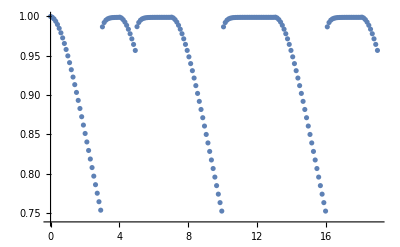

```mathematica
ListPlot[trajectoryLST,DataRange->{0,periods}]
```